注意：这里和MATLAB有相似之处：如果不想输出数据就在结尾加 ；，否则加；
声明变量用小写，库函数首字母大写后 [ ] ,没有严格的数据类型，可以按照意思写就可以，以 cell区分，部分结果四舍五入了，可以扩展精度。

NO.1:

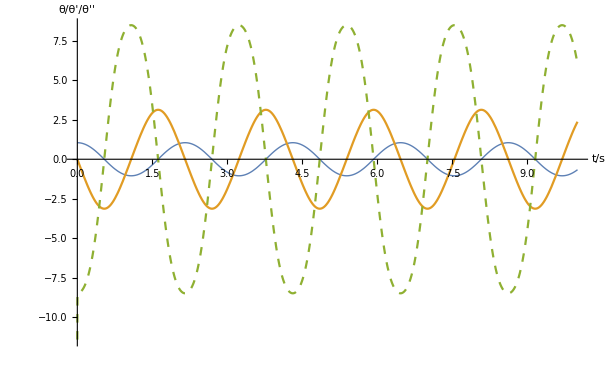

```mathematica
g=9.8;
L=1;
Ω= Sqrt[g / L];
{θ0, ω0}={Pi / 3, 0};
time = 10;
s=NDSolve[{θ''[t]==-Ω^2 * Sin[θ[t]],θ[0]==θ0, θ'[0]==ω0},θ ,{t, 0, time}];
θ=θ /.s[[1]];
Plot[{θ[t],θ'[t],θ''[t]},{t,0,time},AxesLabel->{"t/s", "θ/θ'/θ''"},
PlotStyle->{Thick, Dashing[{}],Dashing[{0.01}]},PlotRange->All]
Clear["Global` *"]
```

NO.2:

{{θ→InterpolatingFunction[{{0., 20.}}, <>]}}

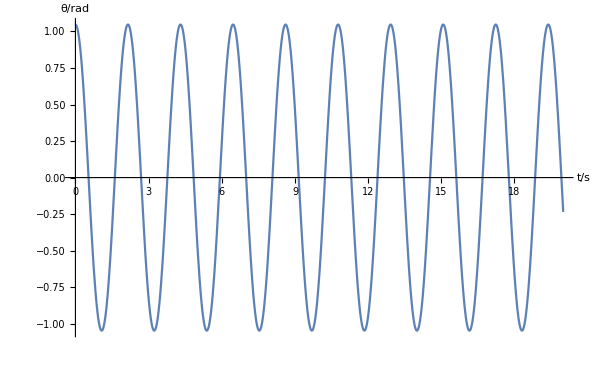

```mathematica
g=9.8;
L=1;
Ω=Sqrt[g/L ];
{θ0, ω0}={Pi/3, 0};
time = 20;
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ,{t,0,time}]
θ=θ/.s[[1]];
Plot[θ[t],{t,0,time},AxesLabel->{"t/s","θ/rad"}]
Clear["Global`*"]
```

NO.3:

```mathematica
g=9.8;
L=1;
Ω=Sqrt[g/L ];
{θ0, ω0}={Pi/3, 0};
time = 20;
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ,{t,0,time}];
θ=θ/.s[[1]];
tm=tp={};
Do[
t1=FindMaximum[θ[t],{t,2.1539728i}];
AppendTo[tm,t1[[1]]];
AppendTo[tp,t/.t1[[2]]],
{i,Floor[time/2.1539728]}
]
(*Do 循环结束*)
Partition[tm,4]//TableForm
tp=Table[tp[[i+1]]-tp[[i]],{i,Length[tm]-1}];
Partition[tp,4]//TableForm
Clear["Global`*"]
```

```mathematica
{{1.047197555069266, 1.0471975187470384, 1.0471975054776832, 1.0471974696709903}, {1.0471974997507074, 1.047197515885273, 1.047197436776684, 1.0471974431830289}}
```

```mathematica
{{2.1539727999999982, 2.1539727650027514, 2.153972817927939, 2.1539727566041016}, {2.1539728202053965, 2.1539727913734517, 2.1539726961185917, 2.153972745085003}}
```

NO.4:

2.00709-2.28045×10^-6 θ+0.0000385184 θ^2-1.7008×10^-8 θ^3+1.12308×10^-9 θ^4-5.99739×10^-12 θ^5+4.56976×10^-14 θ^6

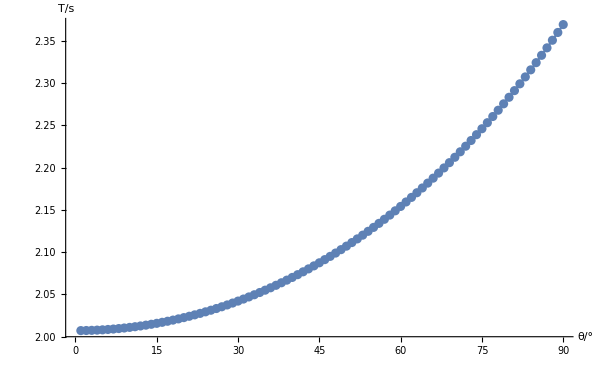

{{1,2.00713},{2,2.00724},{3,2.00743},{4,2.0077},{5,2.00805}}

2.00709

```mathematica
g=9.8;
L=1;
Ω=Sqrt[g/L ];
time = 20;
tc=2.1;
tm={};
Do[
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==θ0 * Pi/180,θ'[0]==0},θ,{t,0,time},MaxStepFraction->0.001];
a=θ/.s[[1]];
t1=FindMaximum[a[t],{t,tc}];
t2=FindMaximum[a[t],{t,2tc}];
tc=(t/.t2[[2]])-(t/.t1[[2]]);
AppendTo[tm,{θ0,tc}],
{θ0,90}
]
(*Do 循环结束*)
g1=ListPlot[tm,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"θ/°","T/s"}];
s=Fit[tm,{1,θ,θ^2,θ^3,θ^4,θ^5,θ^6},θ]
g2=Plot[s,{θ,1,90}];
Show[g1,g2]
Take[tm,5]
2 Pi Sqrt[L/g]
Clear["Global`*"]
```

NO.5:

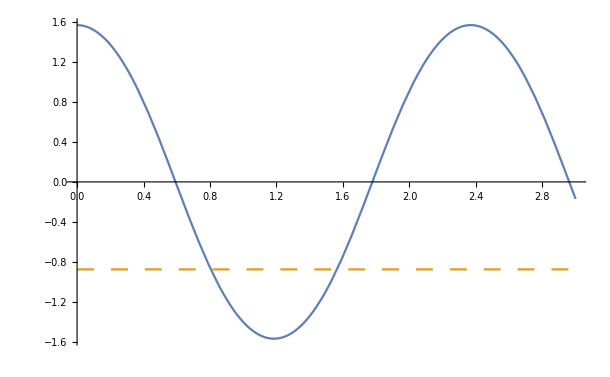

```mathematica
g=9.8;
L=1;
Ω=Sqrt[g/L ];
time = 10;
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==Pi/2,θ'[0]==0},θ,{t,0,time}];
θ=θ/.s[[1]];
t1=FindMinimum[θ[t],{t,2.1}];
T=(t/.t1[[2]]);
a=t1[[1]];
asin=a*Sin[2*Pi/T+Pi/2];
Plot[{θ[t],asin},{t,0,3},PlotStyle->{Dashing[{}],Dashing[{0.02,0.02}]}]
Clear["Global`*"]
```

NO.6:

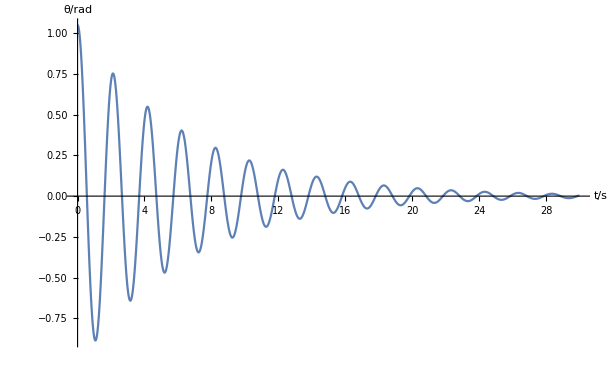

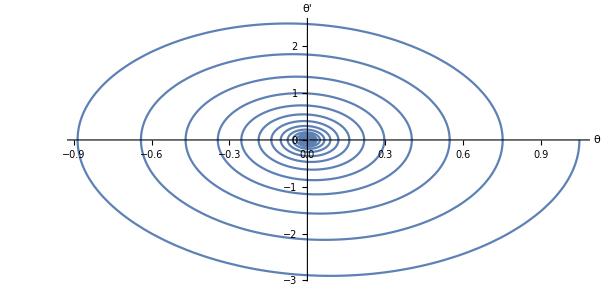

```mathematica
g=9.8;
L=1;
Ω=Sqrt[g/L];
η=0.3;
{θ0,ω0}={Pi/3,0};
time=30;
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]]-η*θ'[t],θ[0]==θ0,θ'[0]==ω0},θ,{t,0,time}];
θ=θ/.s[[1]];
Plot[θ[t],{t,0,time},AxesLabel->{"t/s","θ/rad"},PlotRange->All]
ParametricPlot[{θ[t],θ'[t]},{t,0,time},AxesLabel->{"θ","θ'"},PlotRange->All,AspectRatio->1/2]
Clear["Global`*"]
```

```mathematica
g=9.8;
L=1;
Ω=√(g/L);
η=0.3;
{θ0,ω0}={Pi/3,0};
time=80;
s=NDSolve[{θ''[t]==-Ω^2 Sin[θ[t]]-η*θ'[t],θ[0]==θ0,θ'[0]==ω0},θ,{t,0,time},WorkingPrecision->40,MaxSteps->∞];
θ=θ/.s[[1]];
t0=0;
δt=2.1;
peak={};
Do[
θm=FindMaximum[θ[t],{t,δt+t0}];
AppendTo[peak,{t/.θm[[2]],θm[[1]]}];
t1=t/.θm[[2]];
δt=t1-t0;
t0=t1,
{j,37}
]
(*Do 循环结束*)
peak=Take[peak,-15];
FindFit[peak,a ⅇ^(-b t),{a,b},t]
logpeak=Table[{peak[[i,1]],Log[peak[[i,2]]]},{i,15}];
s=Fit[logpeak,{1,t},t]
{a->ⅇ^s[[1]],b->-s[[2,1]]}
FindFit[logpeak,Log[a]-b t,{a,b},t]
Clear["Global`*"]
```

NO.7:

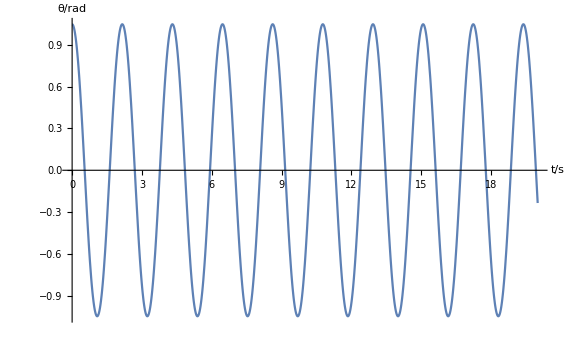

e0= 4.9